```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

24

24

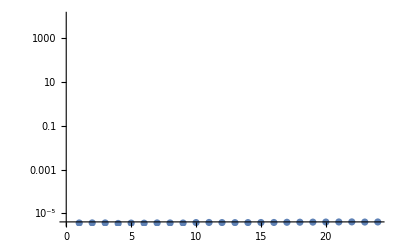

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{1*^4,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|S1EL_xOffset→0.0020274,S1EL_yOffset→0.00210934,S2EL_xOffset→0.00182388,S2EL_yOffset→0.00197763,S2ER_xOffset→0.00192691,S2ER_yOffset→0.00208931,S1ER_xOffset→0.00207665,S1ER_yOffset→0.00201821,PDrive_mean_x→-0.000202633,PDrive_mean_y→5.5451×10^-6,PDrive_sigma_x→0.000174599,PDrive_sigma_y→0.0000212169,PDrive_mean_xp→0.0000281837,PDrive_mean_yp→0.0000297428,PDrive_sigmaSI90_x→0.000156787,PDrive_sigmaSI90_y→0.0000214557,PDrive_emitSI90_x→0.000157075,PDrive_emitSI90_y→9.9556×10^-6,PDrive_zLen→0.0000268771,PDrive_zCentroid→991.332,PWitness_mean_x→-0.0011046,PWitness_mean_y→0.0000155904,PWitness_sigma_x→0.000211486,PWitness_sigma_y→0.0000266811,PWitness_mean_xp→0.000599486,PWitness_mean_yp→0.0000641036,PWitness_sigmaSI90_x→0.000193338,PWitness_sigmaSI90_y→0.0000243541,PWitness_emitSI90_x→0.0000659718,PWitness_emitSI90_y→3.5352×10^-6,PWitness_zLen→0.0000101198,PWitness_zCentroid→991.332,bunchSpacing→0.000204033,transverseCentroidOffset→0.000902021,lostChargeFraction→0.,maximizeMe→4.0367×10^-6|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

S1EL_xOffset : 0.0020274029
S1EL_yOffset : 0.0021093365
S2EL_xOffset : 0.0018238753
S2EL_yOffset : 0.0019776322
S2ER_xOffset : 0.0019269082
S2ER_yOffset : 0.0020893139
S1ER_xOffset : 0.0020766453
S1ER_yOffset : 0.0020182113
PDrive_mean_x : -0.000202633
PDrive_mean_y : 5.5451e-6
PDrive_sigma_x : 0.0001745992
PDrive_sigma_y : 0.0000212169
PDrive_mean_xp : 0.0000281837
PDrive_mean_yp : 0.0000297428
PDrive_sigmaSI90_x : 0.0001567865
PDrive_sigmaSI90_y : 0.0000214557
PDrive_emitSI90_x : 0.0001570747
PDrive_emitSI90_y : 9.9556e-6
PDrive_zLen : 0.0000268771
PDrive_zCentroid : 991.3317130422
PWitness_mean_x : -0.0011045976
PWitness_mean_y : 0.0000155904
PWitness_sigma_x : 0.0002114864
PWitness_sigma_y : 0.0000266811
PWitness_mean_xp : 0.0005994862
PWitness_mean_yp : 0.0000641036
PWitness_sigmaSI90_x : 0.0001933382
PWitness_sigmaSI90_y : 0.0000243541
PWitness_emitSI90_x : 0.0000659718
PWitness_emitSI90_y : 3.5352e-6
PWitness_zLen : 0.0000101198
PWitness_zCentroid : 991.3319170755
bunchSpacing : 0.0002040333
transverseCentroidOffset : 0.0009020205
lostChargeFraction : 0.
maximizeMe : 4.0367e-6

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.000902021

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

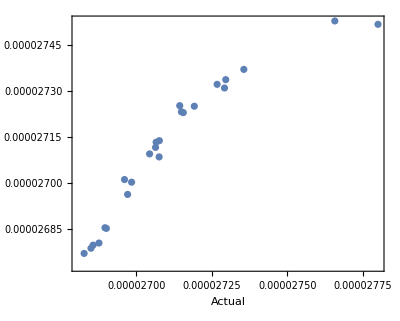

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{S1ELxOffset→Indeterminate,S1ELyOffset→Indeterminate,S1ERxOffset→Indeterminate,S1ERyOffset→Indeterminate,S2ELxOffset→Indeterminate,S2ELyOffset→Indeterminate,S2ERxOffset→Indeterminate,S2ERyOffset→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
S1ELxOffset | 1 | 5.92171×10^-13 | 5.92171×10^-13 | 53.5339 | 2.53966×10^-6
S1ELyOffset | 1 | 1.1289×10^-13 | 1.1289×10^-13 | 10.2055 | 0.00603001
S1ERxOffset | 1 | 1.56121×10^-13 | 1.56121×10^-13 | 14.1138 | 0.00190413
S1ERyOffset | 1 | 2.89173×10^-14 | 2.89173×10^-14 | 2.6142 | 0.126742
S2ELxOffset | 1 | 1.93684×10^-13 | 1.93684×10^-13 | 17.5096 | 0.000797578
S2ELyOffset | 1 | 2.85419×10^-14 | 2.85419×10^-14 | 2.58027 | 0.129045
S2ERxOffset | 1 | 8.44607×10^-14 | 8.44607×10^-14 | 7.63549 | 0.0144949
S2ERyOffset | 1 | 1.74292×10^-16 | 1.74292×10^-16 | 0.0157565 | 0.901775
Error | 15 | 1.65924×10^-13 | 1.10616×10^-14 |  | 
Total | 23 | 1.36288×10^-12 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Plot::plld: Endpoints for x in {x,0.,0.} must have distinct machine-precision numerical values.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[x,{x,Min[lm[Response]],Max[lm[Response]]},PlotStyle→Red]].

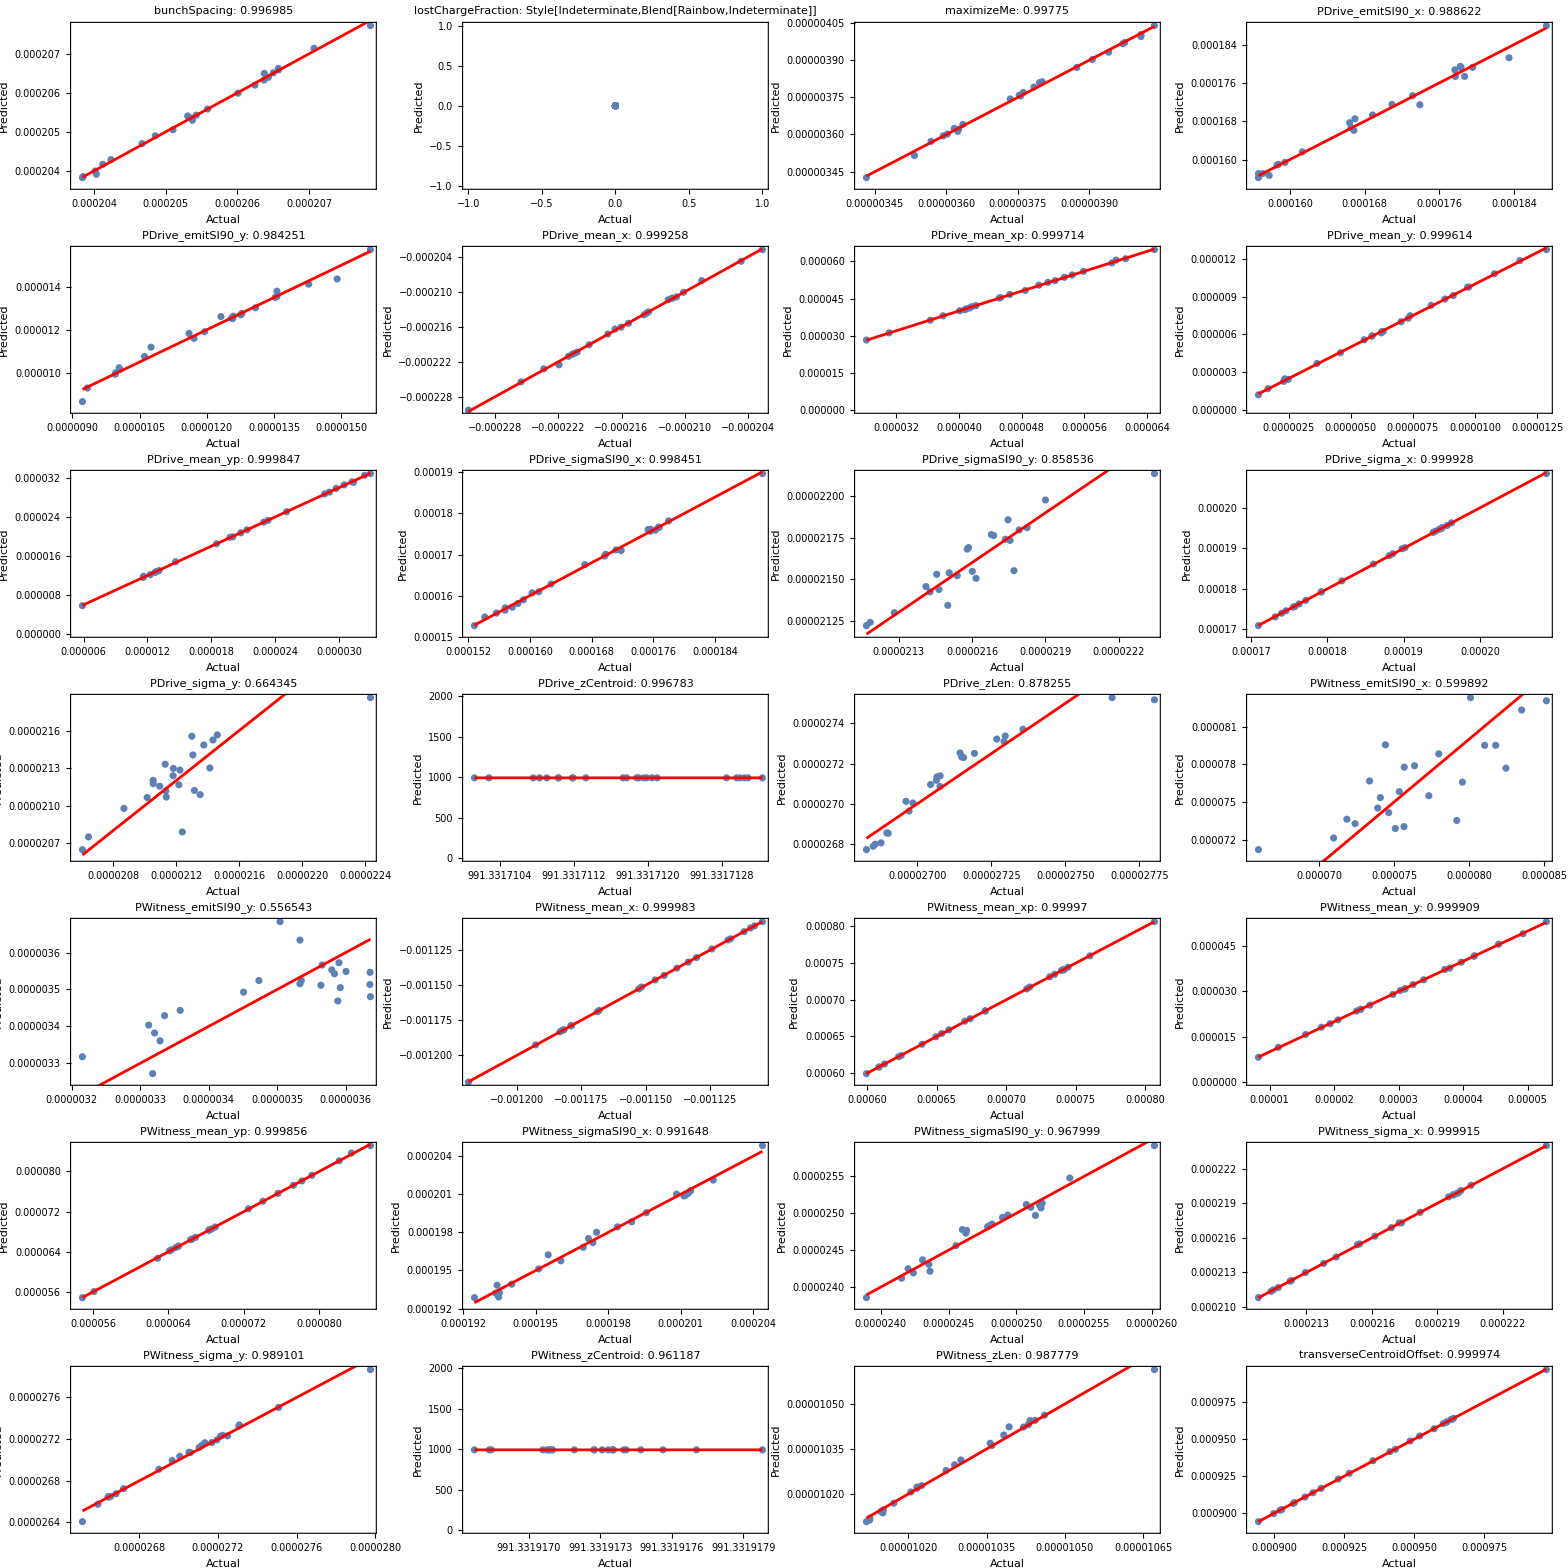

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```